```mathematica
aa={100,10,5,1,0.5,0.1,0.01,0.005(*,0.001*)};
```

```mathematica
αm={{0.01,10},{0.1,1},{0.1,10},{0.01,100},{1,10},{0.1,100}};
```

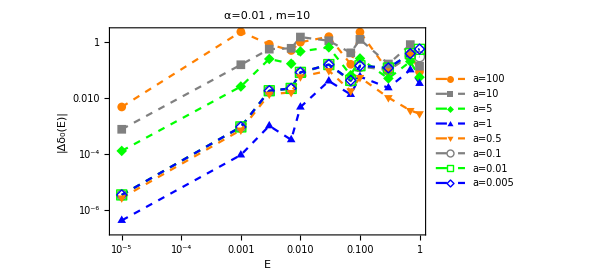
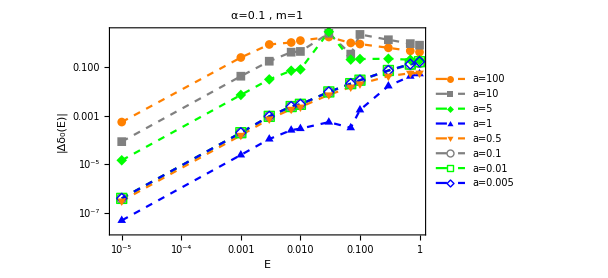
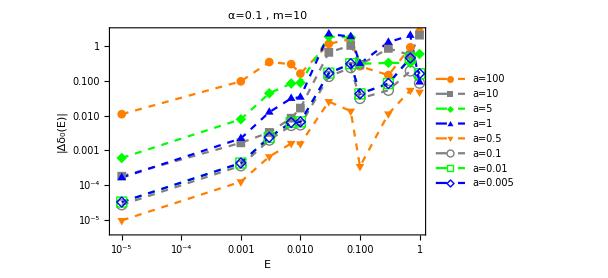
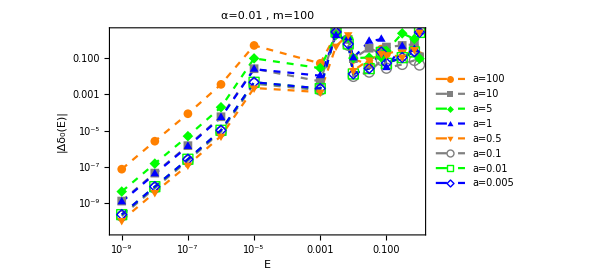
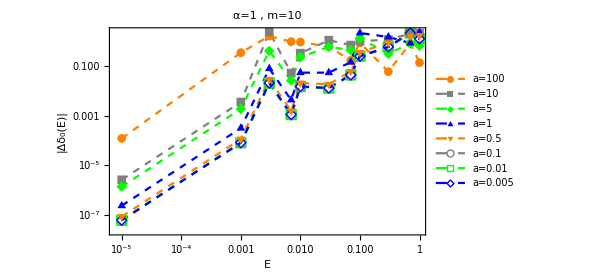
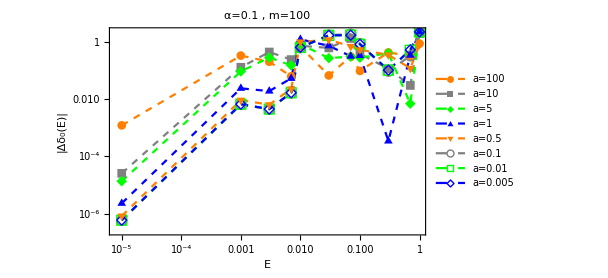

```mathematica
Table[Block[{α,m,ima,La},
{α,m}=αm[[i]];
Get["C:\\Users\\ASUS\\Documents\\SyntheticPotential_"<>"Alpha="<>ToString[α]<>"&m="<>ToString[m]<>".ex"];
ima=ListLogLogPlot[Table[La[[n]],{n,Length@aa}],Frame->True,Joined->True,PlotMarkers->Automatic,ImageSize->450,FrameLabel->{"E","|Δδ_0(E)|"},(*RotateLabel->False,*)PlotStyle->{{Dashed,Orange},{Dashed,Gray},{Dashed,Green},{Dashed,Blue}},PlotLegends->Placed[LineLegend[(("a="<>ToString[#])&/@aa),LegendLayout->{"Column",2}(*,LegendMarkerSize->20*),LegendMargins->{{0,0},{0,0}}(*,LegendFunction->Framed*)],(*{{},{}}*){Right,Bottom}],PlotLabel->Style[("α="<>ToString@α<>" ,  m="<>ToString@m),18],FrameTicksStyle->{{{Bold,12},{}},{{Bold,12},{}}}];
Export[Evaluate["C:\\Users\\ASUS\\OneDrive\\Documents\\Test_6\\Test_Determine_a_Alpha="<>ToString[α]<>"&m="<>ToString[m]<>".eps"],ima];
ima],{i,1,6}]
```

```mathematica
aa={100,10,5,1,0.5,0.1,0.05,0.01};
```

```mathematica
αm={{0.01,10},{0.1,1},{0.1,10},{0.01,100},{1,10},{0.1,100}};
```

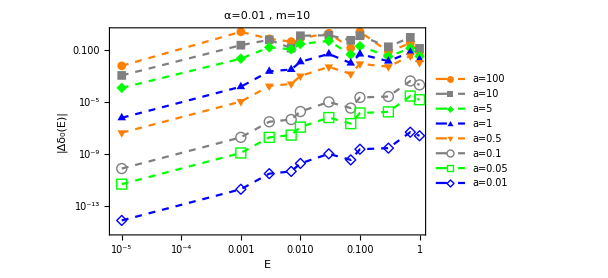
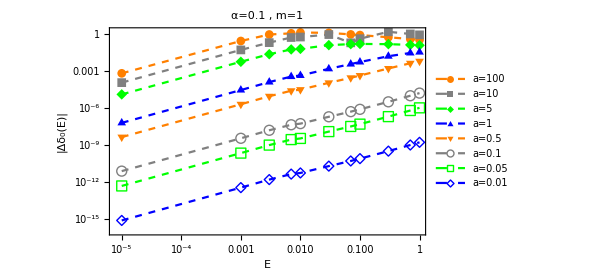
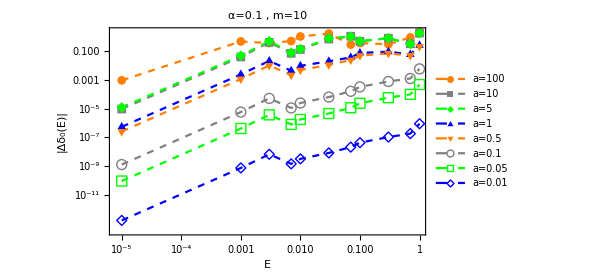
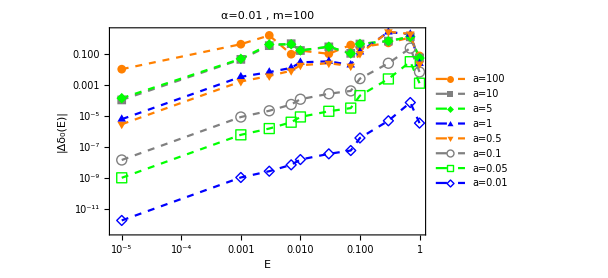
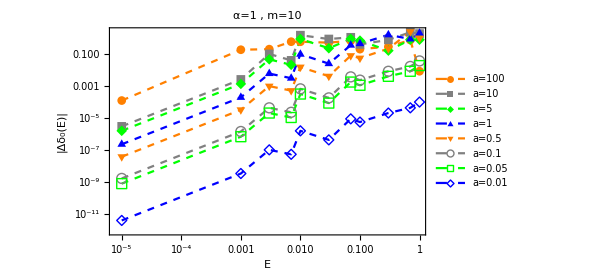
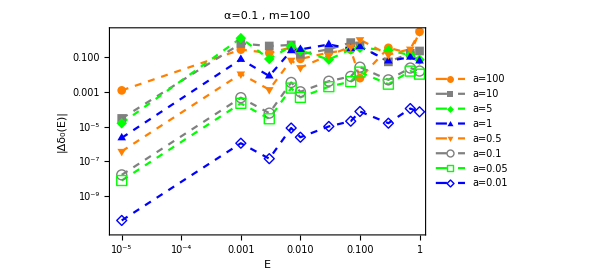

```mathematica
Table[Block[{α,m,ima,La},
{α,m}=αm[[i]];
Get["C:\\Users\\ASUS\\Documents\\CoulombPotential_"<>"Alpha="<>ToString[α]<>"&m="<>ToString[m]<>".ex"];
ima=ListLogLogPlot[Table[La[[n]],{n,Length@aa}],Frame->True,Joined->True,PlotMarkers->Automatic,ImageSize->450,FrameLabel->{"E","|Δδ_0(E)|"},(*RotateLabel->False,*)PlotStyle->{{Dashed,Orange},{Dashed,Gray},{Dashed,Green},{Dashed,Blue}},PlotLegends->Placed[LineLegend[(("a="<>ToString[#])&/@aa),LegendLayout->{"Column",2}(*,LegendMarkerSize->20*),LegendMargins->{{0,0},{0,0}}(*,LegendFunction->Framed*)],(*{{},{}}*){Right,Bottom}],PlotLabel->Style[("α="<>ToString@α<>" ,  m="<>ToString@m),18],FrameTicksStyle->{{{Bold,12},{}},{{Bold,12},{}}}];
Export[Evaluate["C:\\Users\\ASUS\\OneDrive\\Documents\\Test_6\\Test_Determine_Coulomb_a_Alpha="<>ToString[α]<>"&m="<>ToString[m]<>".eps"],ima];
ima],{i,1,6}]
```